```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
transeries=Transpose[series];
transeries=Drop[transeries,1];
Dimensions[transeries]
hopdates=Drop[series[[1]],4]
%//Length
countriescsv=transeries[[1]];
%//Dimensions
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

{92,265}

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20,4/19/20}

89

{265}

```mathematica
TableForm[transeries]
```

1
 |  |  |  |

```mathematica
countinds=Flatten[Position[countriescsv,"Canada"]]
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}]
```

{37,38,39,40,41,42,43,44,45,46,47,233,240,247,248}

{{{2020,1,22},0},{{2020,1,23},0},{{2020,1,24},0},{{2020,1,25},0},{{2020,1,26},1},{{2020,1,27},1},{{2020,1,28},2},{{2020,1,29},2},{{2020,1,30},2},{{2020,1,31},4},{{2020,2,1},4},{{2020,2,2},4},{{2020,2,3},4},{{2020,2,4},4},{{2020,2,5},5},{{2020,2,6},5},{{2020,2,7},7},{{2020,2,8},7},{{2020,2,9},7},{{2020,2,10},7},{{2020,2,11},7},{{2020,2,12},7},{{2020,2,13},7},{{2020,2,14},7},{{2020,2,15},7},{{2020,2,16},7},{{2020,2,17},8},{{2020,2,18},8},{{2020,2,19},8},{{2020,2,20},8},{{2020,2,21},9},{{2020,2,22},9},{{2020,2,23},9},{{2020,2,24},10},{{2020,2,25},11},{{2020,2,26},11},{{2020,2,27},13},{{2020,2,28},14},{{2020,2,29},20},{{2020,3,1},24},{{2020,3,2},27},{{2020,3,3},30},{{2020,3,4},33},{{2020,3,5},37},{{2020,3,6},49},{{2020,3,7},54},{{2020,3,8},64},{{2020,3,9},77},{{2020,3,10},79},{{2020,3,11},108},{{2020,3,12},117},{{2020,3,13},193},{{2020,3,14},198},{{2020,3,15},252},{{2020,3,16},415},{{2020,3,17},478},{{2020,3,18},657},{{2020,3,19},800},{{2020,3,20},943},{{2020,3,21},1277},{{2020,3,22},1469},{{2020,3,23},2088},{{2020,3,24},2790},{{2020,3,25},3251},{{2020,3,26},4042},{{2020,3,27},4682},{{2020,3,28},5576},{{2020,3,29},6280},{{2020,3,30},7398},{{2020,3,31},8527},{{2020,4,1},9560},{{2020,4,2},11284},{{2020,4,3},12437},{{2020,4,4},12978},{{2020,4,5},15756},{{2020,4,6},16563},{{2020,4,7},17872},{{2020,4,8},19141},{{2020,4,9},20654},{{2020,4,10},22059},{{2020,4,11},23316},{{2020,4,12},24298},{{2020,4,13},25679},{{2020,4,14},27034},{{2020,4,15},28208},{{2020,4,16},30808},{{2020,4,17},32813},{{2020,4,18},34355},{{2020,4,19},35632}}

```mathematica
truncdatesandata=Select[datesanddata,#[[2]]>100&]
%//Length
```

{{{2020,3,11},108},{{2020,3,12},117},{{2020,3,13},193},{{2020,3,14},198},{{2020,3,15},252},{{2020,3,16},415},{{2020,3,17},478},{{2020,3,18},657},{{2020,3,19},800},{{2020,3,20},943},{{2020,3,21},1277},{{2020,3,22},1469},{{2020,3,23},2088},{{2020,3,24},2790},{{2020,3,25},3251},{{2020,3,26},4042},{{2020,3,27},4682},{{2020,3,28},5576},{{2020,3,29},6280},{{2020,3,30},7398},{{2020,3,31},8527},{{2020,4,1},9560},{{2020,4,2},11284},{{2020,4,3},12437},{{2020,4,4},12978},{{2020,4,5},15756},{{2020,4,6},16563},{{2020,4,7},17872},{{2020,4,8},19141},{{2020,4,9},20654},{{2020,4,10},22059},{{2020,4,11},23316},{{2020,4,12},24298},{{2020,4,13},25679},{{2020,4,14},27034},{{2020,4,15},28208},{{2020,4,16},30808},{{2020,4,17},32813},{{2020,4,18},34355},{{2020,4,19},35632}}

40

```mathematica
justdata=Transpose[truncdatesandata][[2]]
justtime=Table[i,{i,Length[justdata]}];
jstartdate=truncdatesandata[[1,1]]-{0,0,1}
```

{108,117,193,198,252,415,478,657,800,943,1277,1469,2088,2790,3251,4042,4682,5576,6280,7398,8527,9560,11284,12437,12978,15756,16563,17872,19141,20654,22059,23316,24298,25679,27034,28208,30808,32813,34355,35632}

{2020,3,10}

```mathematica
jdp0={Max[justdata] ,300,0.2}
```

{35632,300,0.2}

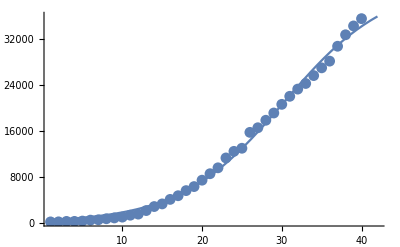

```mathematica
showplots[justdata,jdp0,justtime]
```

```mathematica
{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime]
```

{{41860.4,392.058,0.154269},12,7.90239×10^-7,40}

{51190.4,852.459,0.121643}

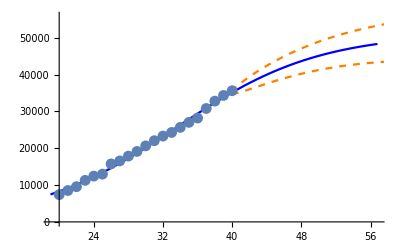
{-Graphics-,1307.,607.551,1277,-6.4726,69.6068}

```mathematica
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,21,justtime,{1,0}];
jp20
jpdata20=justdata[[-21;;]];
datastats[jpdata20,jp20,1.8,2,justtime[[-21;;]]]
```

```mathematica
estimates[justdata,jdp0,21,justtime];
```

{14687.8,80.8089,0.261312}

{51190.4,852.459,0.121643}

{14687.8,80.8089,0.261312}

{51190.4,852.459,0.121643}

{51190.4,852.459,0.121643}

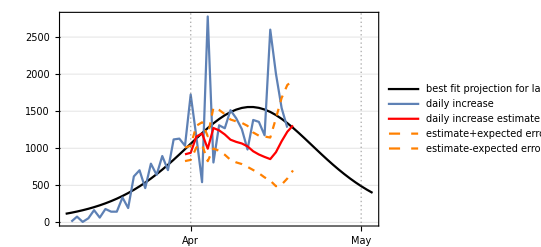
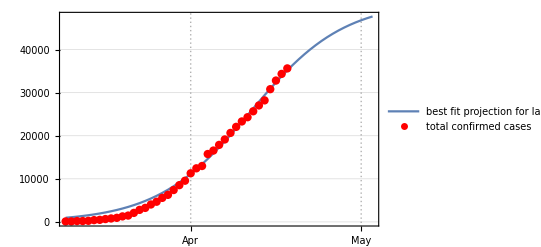
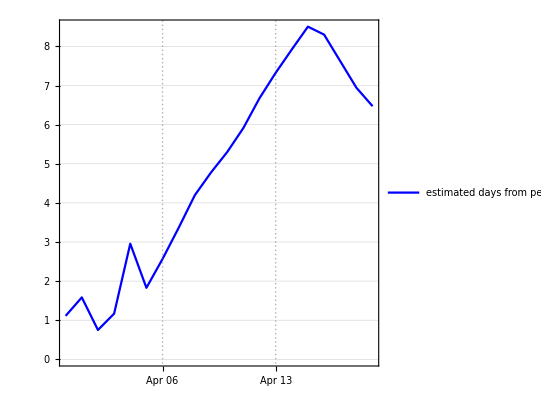
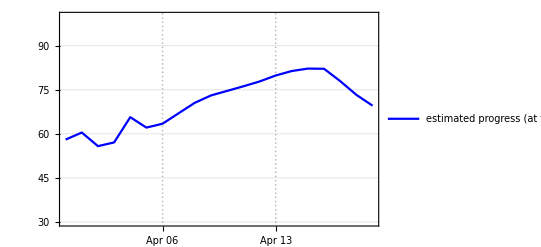

```mathematica
{jgraf,jloggraf,jdfpplot,jprogplot}=somegraphs[jdp0,jp20,justtime,justdata,jstartdate,21,14,0]
```

```mathematica
?GNiteration
```

Global`GNiteration

GNiteration[data_,ip0_,time_]:=Module[{k,tol,maxk,err,p0,np0,convnot,a,b,c},maxk=50;k=0;tol=1/10^6;err=1;p0=ip0;convnot=False;While[k<maxk&&err>tol&&!convnot,k=k+1;{a,b,c}=p0-PseudoInverse[dwf[p0,time,data]].wf[p0,time,data];err=Norm[{a,b,c}-p0];p0={a,b,c};convnot=a<-10^6||a>10^10||c<-100||c>100;];If[convnot,p0={1,1,1}];{p0,k,err,Length[data]}]
 
GNiteration[data_,ip0_]:=Module[{time},time=Table[i,{i,1,Length[data]}];GNiteration[data,ip0,time]]